```mathematica
hourlyBostonTemperatureTimeSeriesResample=TimeSeriesResample[WeatherData["KBOS","Temperature",{{2012,9,1},{2019,6,31}}],"Hour"]
```

TemporalData[TimeSeries, <<1>>]

```mathematica
Export["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\hourlyBostonTemperatureTimeSeriesResample2.wxf", hourlyBostonTemperatureTimeSeriesResample]
```

C:\Users\kylem\Documents\GitHub\2019-WSS\Final Project\Drafts\kyle\hourlyBostonTemperatureTimeSeriesResample2.wxf

```mathematica
RegularlySampledQ[hourlyBostonTemperatureTimeSeriesResample]
```

True

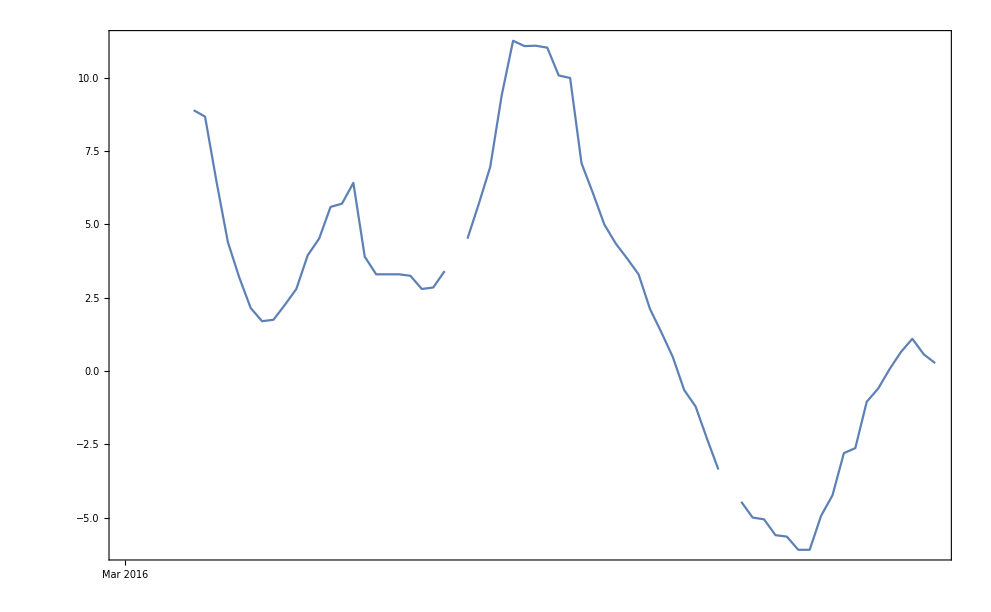

```mathematica
DateListPlot[TimeSeriesWindow[hourlyBostonTemperatureTimeSeriesResample,{DateObject[{2016,3,1}],DateObject[{2016,3,3}]}]]
```